```mathematica
TextCases[IntegerName@Range[49],___~~"i"~~___~~"e"~~___]
```

{{},{},{},{},{five},{},{},{},{nine},{},{},{},{thirteen},{},{fifteen},{sixteen},{},{eighteen},{nineteen},{},{},{},{},{},{twenty-five},{},{},{},{twenty-nine},{},{thirty-one},{},{thirty-three},{},{thirty-five},{},{thirty-seven},{thirty-eight},{thirty-nine},{},{},{},{},{},{forty-five},{},{},{},{forty-nine}}

```mathematica
Range[9]//.{a___,b_,c_,d___}/;Abs[b-c]==1->{a,b,d,c}
```

{1,3,5,7,9,2,4,6,8}

```mathematica
FindFit
```

```mathematica
dat1=Range[12]+RandomReal[{-1,1},12]
```

{1.59145,1.2994,3.84689,4.1738,4.47149,6.74067,7.96948,7.35002,9.65639,9.69636,10.1265,11.3074}

```mathematica
dat2=dat1^3+RandomReal[{-1,1},12]
```

{4.53028,2.52143,57.6324,72.7935,89.8818,306.345,506.807,396.67,901.152,910.788,1039.14,1445.19}

```mathematica
datt={dat1,dat2}ᵀ
```

{{1.59145,4.53028},{1.2994,2.52143},{3.84689,57.6324},{4.1738,72.7935},{4.47149,89.8818},{6.74067,306.345},{7.96948,506.807},{7.35002,396.67},{9.65639,901.152},{9.69636,910.788},{10.1265,1039.14},{11.3074,1445.19}}

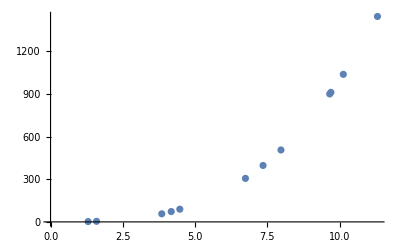

```mathematica
graph=ListPlot[datt]
```

```mathematica
pares=
```

```mathematica
ajus=FindFit[dat1,a x^3+b x^2+c x+d,{a,b,c,d},x]
```

{a→-0.00376234,b→0.0523453,c→0.801314,d→0.382754}

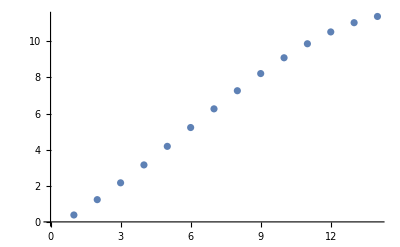

```mathematica
graphr=ListPlot@Table[a x^3+b x^2+c x+d/.ajus,{x,0,13}]
```

```mathematica
fun=Interpolation[datt]
```

InterpolatingFunction[…]

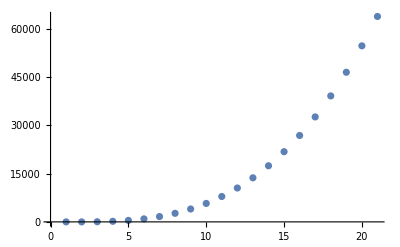

```mathematica
graph2=ListPlot@Table[HermiteH[3,x],{x,0,20}]
```

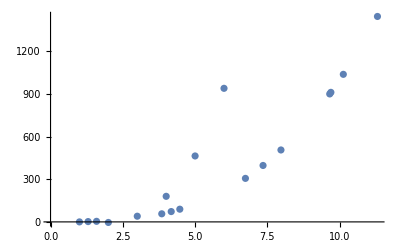

```mathematica
Show[graph,graph2]
```

```mathematica
num=NDSolve[{x'[t]+x[t]==Exp[4t],x[0]==1},x,{t,0,.5}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
ansol=x/.num
```

{InterpolatingFunction[…]}

```mathematica
der=DSolve[{x'[t]+x[t]==Exp[4t],x[0]==1},x[t],t]
```

{{x[t]→1/5 ⅇ^-t (4+ⅇ^(5 t))}}

```mathematica
ec=x[t]/.der[[1]]
```

1/5 ⅇ^-t (4+ⅇ^(5 t))

```mathematica
data={{100,-160},{400,9.},{500,16.9},{600,21.3}}
```

{{100,-160},{400,9.},{500,16.9},{600,21.3}}

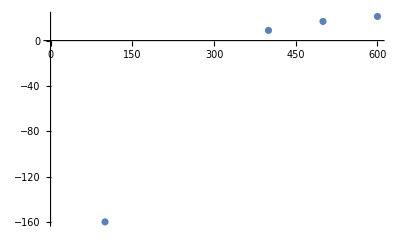

```mathematica
ListPlot[data]
```

```mathematica
tem=Interpolation[data]
```

InterpolatingFunction[…]

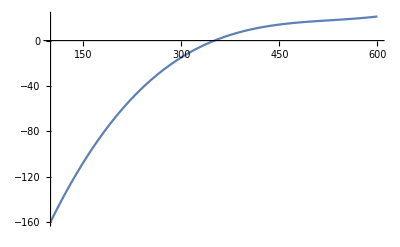

```mathematica
Plot[tem[t],{t,100,600}]
```

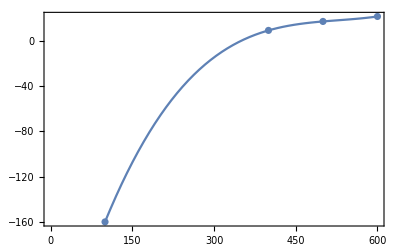

```mathematica
Show[ListPlot[data],Plot[tem[t],{t,100,600}],Frame->True]
```

```mathematica
tem[450]
```

14.1644

```mathematica
(*Ajuste lineal*)
```

```mathematica
f[x_]:=a Exp[x/b]
```

```mathematica
datos=Table[{x,f[x]/.{a->2,b->3}},{x,0,10}]
```

{{0,2},{1,2 ⅇ^(1/3)},{2,2 ⅇ^(2/3)},{3,2 ⅇ},{4,2 ⅇ^(4/3)},{5,2 ⅇ^(5/3)},{6,2 ⅇ^2},{7,2 ⅇ^(7/3)},{8,2 ⅇ^(8/3)},{9,2 ⅇ^3},{10,2 ⅇ^(10/3)}}

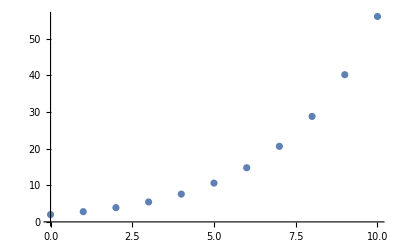

```mathematica
ListPlot[datos]
```

```mathematica
fit=FindFit[datos,{1,x,x^2},x]
```

FindFit::argrx: FindFit called with 3 arguments; 4 arguments are expected.

FindFit[{{0,2},{1,2 ⅇ^(1/3)},{2,2 ⅇ^(2/3)},{3,2 ⅇ},{4,2 ⅇ^(4/3)},{5,2 ⅇ^(5/3)},{6,2 ⅇ^2},{7,2 ⅇ^(7/3)},{8,2 ⅇ^(8/3)},{9,2 ⅇ^3},{10,2 ⅇ^(10/3)}},{1,x,x^2},x]